```mathematica
path = FileNameJoin[Drop[#,Flatten@{Position[#,"Master"]+1,-1}]&@StringSplit[NotebookDirectory[],"\\"]];
ClearAll[data27]
data27=Table[Import[path<>"\\Data\\2015\\April\\27\\27apr_"<>ToString[i]<>"ac.dat"],{i,1,7}];
```

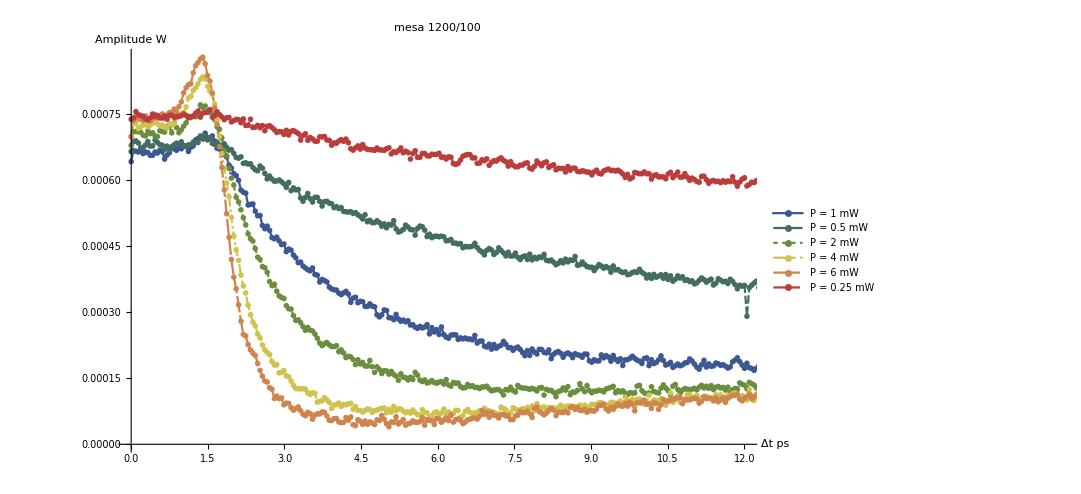

```mathematica
ListLinePlot[Table[data27[[i]][[All,{3,2}]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW","P = 0.25 mW"},ImageSize->800,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,12},All},PlotStyle->"DarkRainbow"]
```

## Выравнивание

```mathematica
Table[data27[[i]][[1,2]],{i,1,7}]
```

{0.000641143,0.000663952,0.00067781,0.000699,0.000697238,0.000737048,0.000728417}

```mathematica
Position[Table[data27[[i]][[1,2]],{i,1,7}],Max[Table[data27[[i]][[1,2]],{i,1,7}]]]
```

{{6}}

```mathematica
amplitude=Table[data27[[i]][[All,2]]*data27[[6]][[1,2]]/data27[[i]][[1,2]],{i,1,7}];
```

```mathematica
newData27=Table[Transpose[{data27[[i]][[All,3]],Log[amplitude[[i]]]}],{i,1,7}];
```

```mathematica
allLogData27=Table[Transpose[{Log[data27[[i]][[All,3]]],Log[amplitude[[i]]]}],{i,1,7}];
```

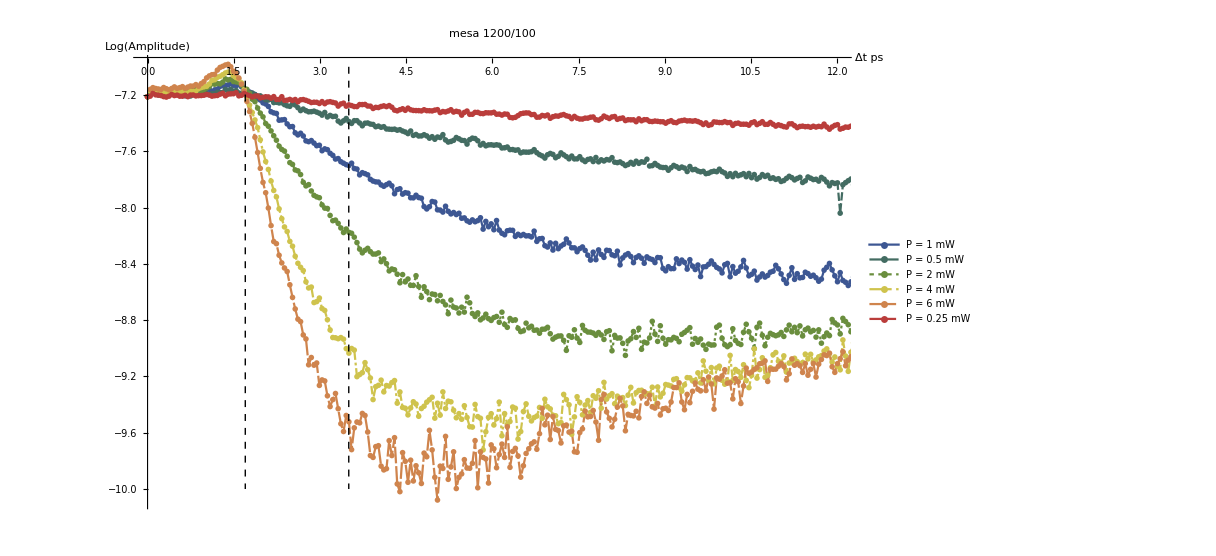

```mathematica
Show[ListLinePlot[Table[newData27[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Log(Amplitude)"},LabelStyle->18,PlotRange->{{0,12},All},PlotStyle->"DarkRainbow"],Graphics[{Black,Dashed,Line[{{{1.7,-7},{1.7,-10}},{{3.5,-7},{3.5,-10}}}]}]]
```

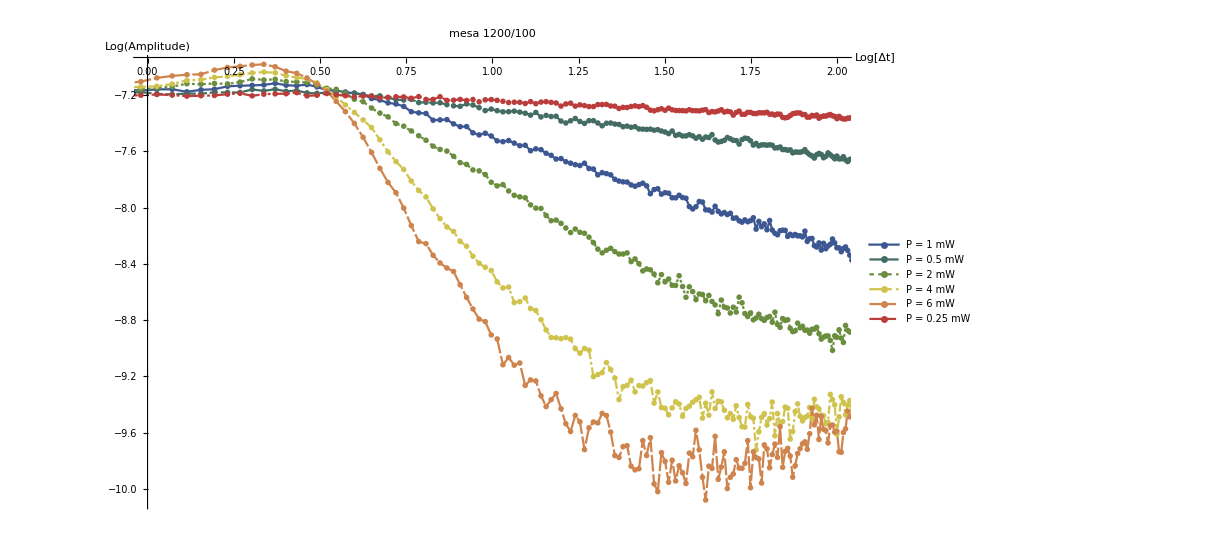

```mathematica
ListLinePlot[Table[allLogData27[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Log[Δt]","Log(Amplitude)"},LabelStyle->18,PlotRange->{{0,2},All},PlotStyle->"DarkRainbow"]
```

## Отрубаю лишнее для прологорифмированных полностью.

```mathematica
Dimensions[allLogData27[[1]]]
```

{300,2}

```mathematica
Count[allLogData27[[1]][[All,1]],u_/;u<0.6]
```

39

```mathematica
Count[allLogData27[[1]][[All,1]],u_/;u>0.8]
```

252

```mathematica
perfectPart=Table[Drop[Drop[allLogData27[[i]],-252],39],{i,1,5}];
```

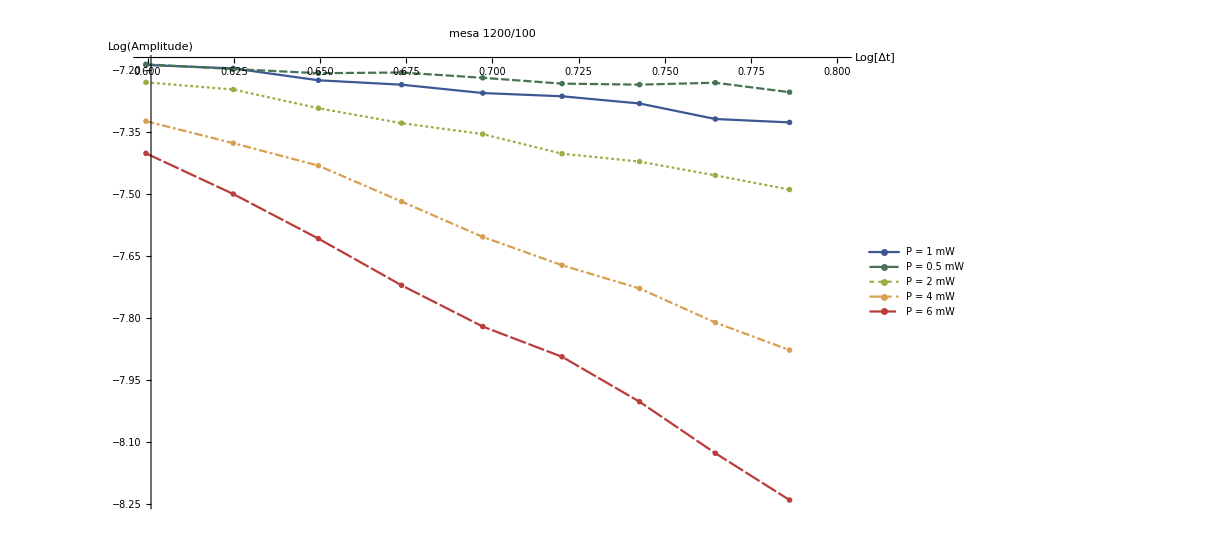

```mathematica
ListLinePlot[Table[perfectPart[[i]],{i,1,5}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Log[Δt]","Log(Amplitude)"},LabelStyle->18,PlotRange->{{0.6,.8},All},PlotStyle->"DarkRainbow"]
```

```mathematica
perfectPart[[1]]
```

{{0.599536,-7.18828},{0.624854,-7.19665},{0.649546,-7.22541},{0.673644,-7.23608},{0.697175,-7.25627},{0.720164,-7.26414},{0.742637,-7.28156},{0.764616,-7.31918},{0.786122,-7.32739}}

```mathematica
coeff=Table[FindFit[perfectPart[[i]],a t+b,{a,b},t],{i,1,5}]
```

{{a→-0.759641,b→-6.72677},{a→-0.323017,b→-6.99473},{a→-1.42558,b→-6.36726},{a→-3.04919,b→-5.47423},{a→-4.431,b→-4.73254}}

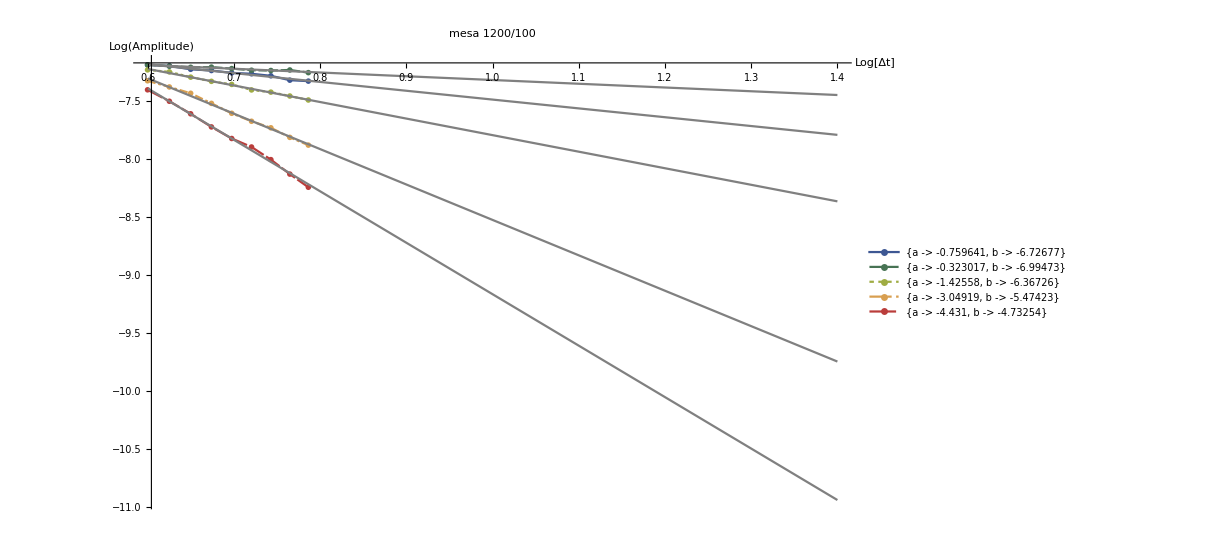

```mathematica
Show[ListLinePlot[Table[perfectPart[[i]],{i,1,5}],PlotLegends->Table[ToString@coeff[[i]],{i,1,5}],ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Log[Δt]","Log(Amplitude)"},LabelStyle->18,PlotRange->{{0.6,1.4},All},PlotStyle->"DarkRainbow"],Plot[Table[a x+b/.coeff[[i]],{i,1,5}],{x,0.6,1.4},PlotStyle->Gray],PlotRange->{{0.6,.8},{-7.1,-8.5}}]
```

```mathematica
FullForm[coeff]
```

List[List[Rule[a,-0.759641],Rule[b,-6.72677]],List[Rule[a,-0.323017],Rule[b,-6.99473]],List[Rule[a,-1.42558],Rule[b,-6.36726]],List[Rule[a,-3.04919],Rule[b,-5.47423]],List[Rule[a,-4.431],Rule[b,-4.73254]]]

```mathematica
coeff[[1,1,2]]
```

-0.759641

```mathematica
power={1,0.5,2,4,6,0.25}
```

{1,0.5,2,4,6,0.25}

```mathematica
powerNew = Sort[Table[{power[[i]],coeff[[i,1,2]]},{i,1,5}]]
```

{{0.5,-0.323017},{1,-0.759641},{2,-1.42558},{4,-3.04919},{6,-4.431}}

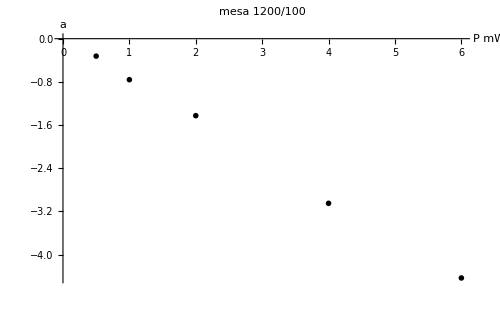

```mathematica
ListPlot[Sort[Table[{power[[i]],coeff[[i,1,2]]},{i,1,5}]],ImageSize->500,PlotLabel->"mesa 1200/100",AxesLabel->{"P mW","a"},LabelStyle->15,AxesStyle->Thick]
```

## Аппроксимация полиномом 2^ой степени

```mathematica
coefNew = FindFit[powerNew,a t^2+b t+ c,{a,b,c},t]
```

{a→0.00800658,b→-0.801134,c→0.0737012}

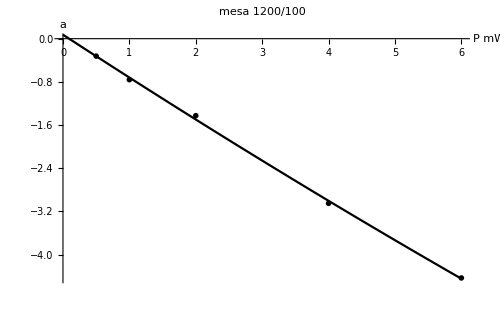

```mathematica
Show[ListPlot[Sort[Table[{power[[i]],coeff[[i,1,2]]},{i,1,5}]],ImageSize->500,PlotLabel->"mesa 1200/100",AxesLabel->{"P mW","a"},LabelStyle->15,AxesStyle->Thick],
Plot[a x^2 + b x + c/.coefNew,{x,0,6}]]
```

## Данамика изменения коэффициента наклона (производная)

## Усреднение по заданному количеству точек

```mathematica
diffNumber[list_,averege_] := With[{dif = Table[{list[[i]][[1]],(list[[i+1]][[2]]-list[[i-1]][[2]])/(list[[i]][[1]]-list[[i-1]][[1]])},{i,2,Length[list]-1}]},
Transpose[{dif[[All,1]],MeanFilter[dif[[All,2]],averege]}]]
```

```mathematica
difData20 = Table[diffNumber[newData27[[i]],20],{i,1,Length[newData27]}];
```

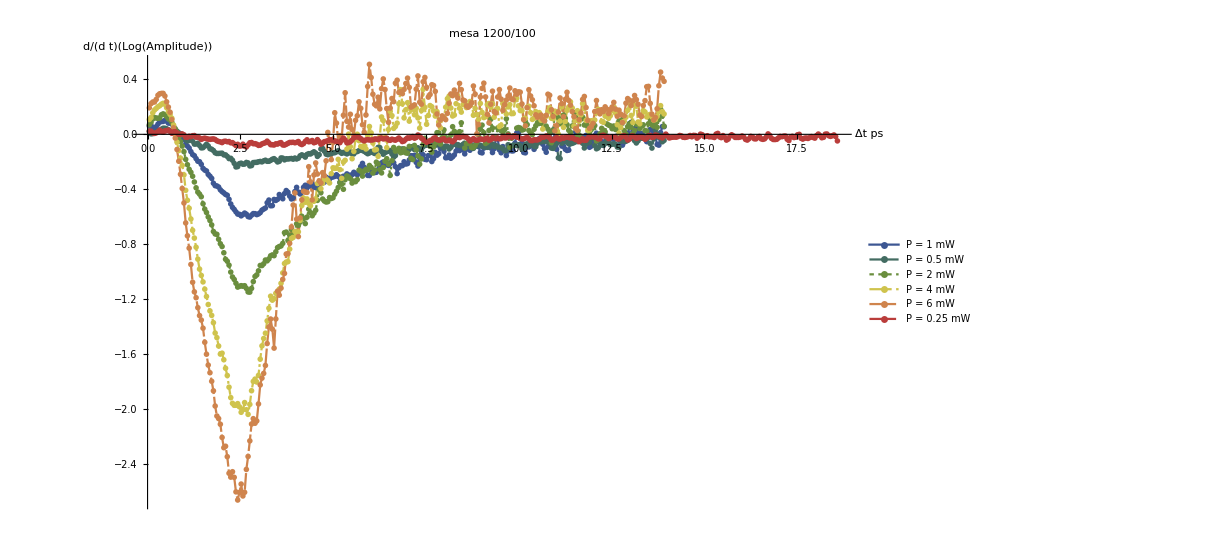

```mathematica
ListLinePlot[Table[difData20[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},
ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","d/(d t)(Log(Amplitude))"},LabelStyle->18,PlotRange->All,PlotStyle->"DarkRainbow"]
```

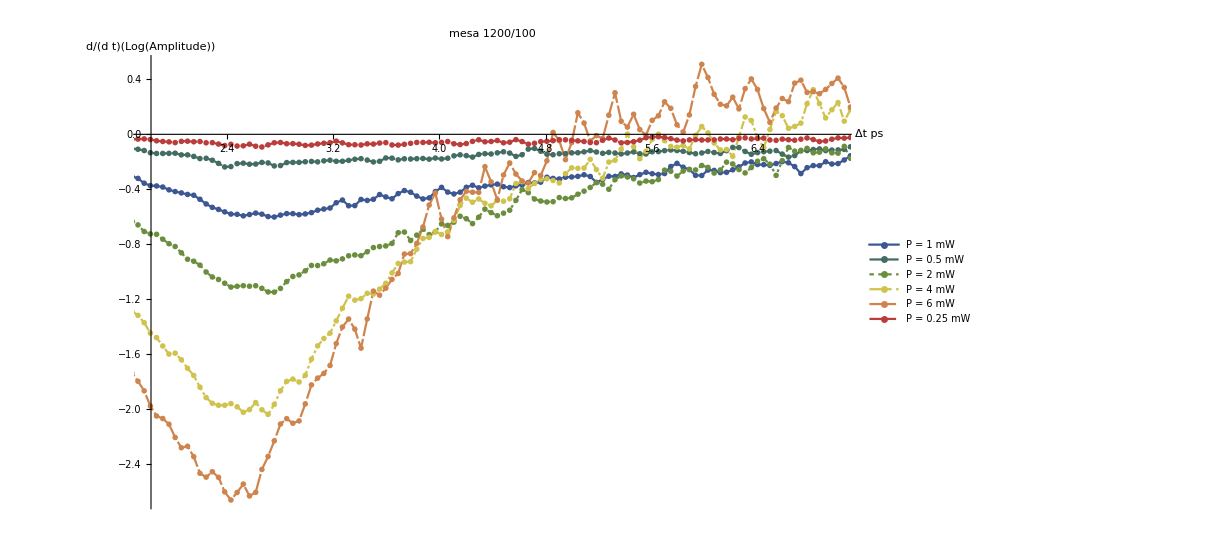

```mathematica
ListLinePlot[Table[difData20[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},
ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","d/(d t)(Log(Amplitude))"},LabelStyle->18,PlotRange->{{1.8,7},All},PlotStyle->"DarkRainbow"]
```

```mathematica
difLogData20 = Table[diffNumber[allLogData27[[i]],20],{i,1,Length[allLogData27]}];
```

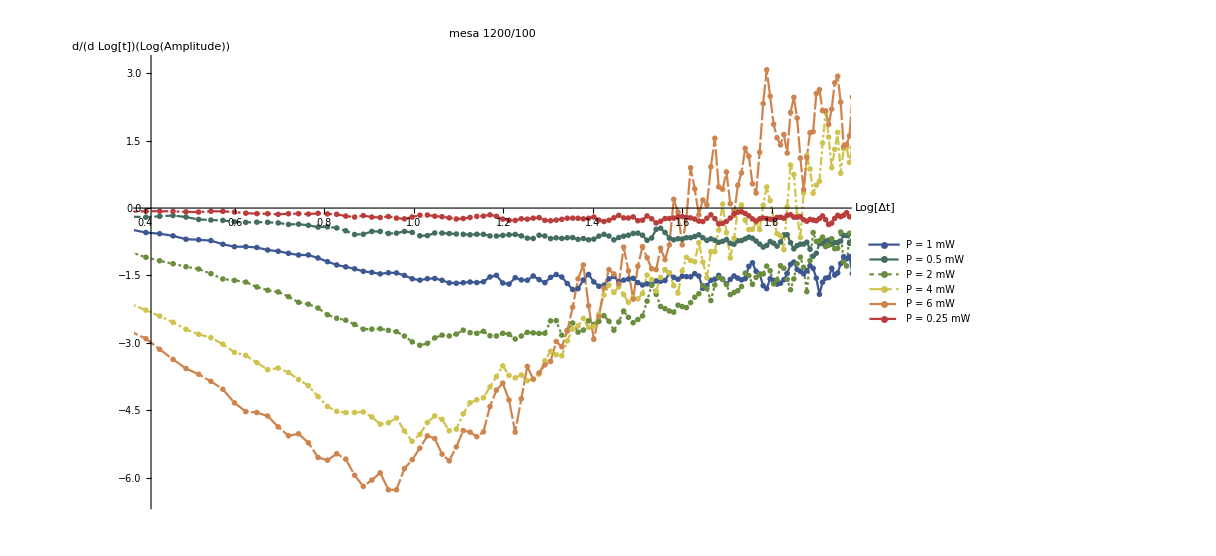

```mathematica
ListLinePlot[Table[difLogData20[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},
ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Log[Δt]","d/(d Log[t])(Log(Amplitude))"},LabelStyle->18,PlotRange->{{Log[1.5],Log[7]},{-6.5,3.2}},PlotStyle->"DarkRainbow"]
```

## После изменения временной шкалы (сдвижка).

```mathematica
nonLogorifmicTime = 
  Table[Transpose[{data27[[i]][[All, 3]]-1.68, Log@amplitude[[i]]}], {i, 
    1, 7}];
```

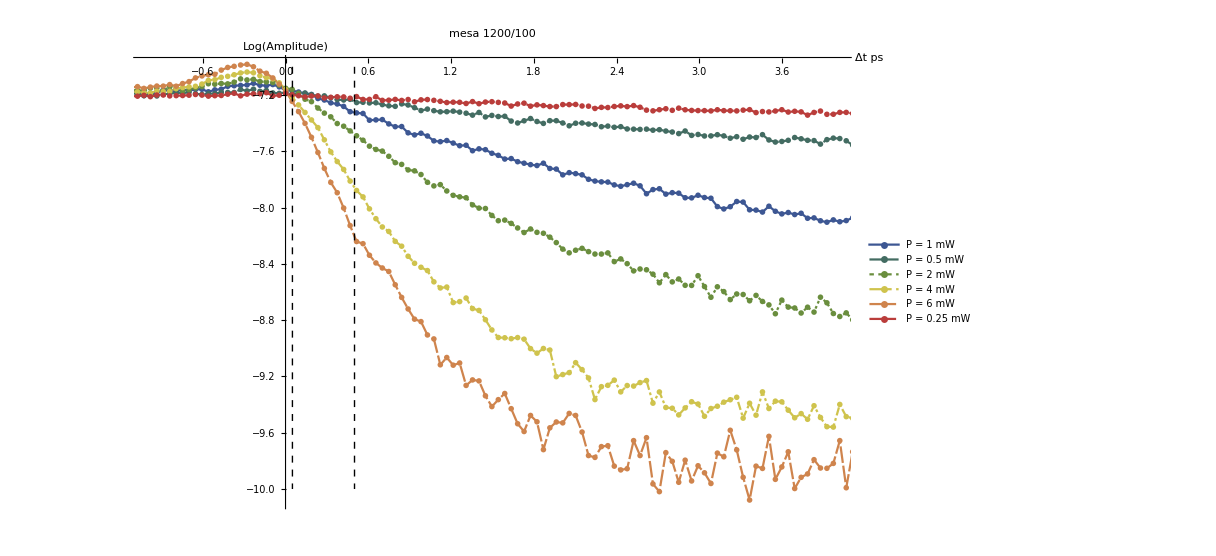

```mathematica
Show[
	ListLinePlot[
		Table[
			nonLogorifmicTime[[i]],{i,1,6}
			],
		PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},
		ImageSize->900,
		PlotLabel->"mesa 1200/100",
		AxesLabel->{"Δt ps","Log(Amplitude)"},
		LabelStyle->18,
		PlotRange->{{-1,4},All},
		PlotStyle->"DarkRainbow"],
	Graphics[
		{Black,Dashed,Line[{{{.05,-7},{.05,-10}},{{.5,-7},{.5,-10}}}]}
	]
]
```

```mathematica
allLog = 
  Log@Table[Transpose[{data27[[i]][[All, 3]]-1.68, amplitude[[i]]}], {i, 
    1, 7}];
```

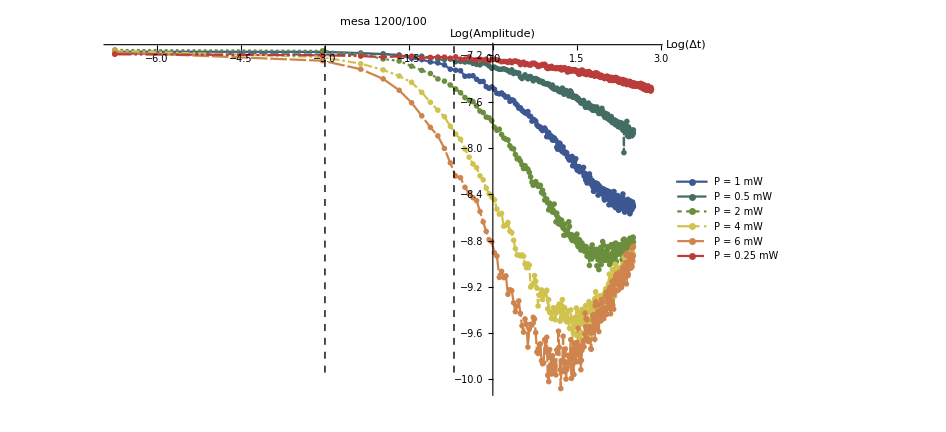

```mathematica
Show[
	ListLinePlot[
		Table[
			allLog[[i]],{i,1,6}
			],
		PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},
		ImageSize->700,
		PlotLabel->"mesa 1200/100",
		AxesLabel->{"Log(Δt)","Log(Amplitude)"},
		LabelStyle->18,
		PlotRange->All,
		PlotStyle->"DarkRainbow"],
	Graphics[
		{Black,Dashed,Line[{{{Log[.05],-7},{Log[.05],-10}},{{Log@.5,-7},{Log@.5,-10}}}]}
	]
]
```

## Анализ зависимости коэффициента наклона от мощьности

```mathematica
Count[nonLogorifmicTime[[1]][[All,1]],u_/;u<0]
```

36

```mathematica
Count[nonLogorifmicTime[[1]][[All,1]],u_/;u>.5]
```

253

```mathematica
perfectPart=Table[Drop[Drop[nonLogorifmicTime[[i]],-252],36],{i,1,5}];
```

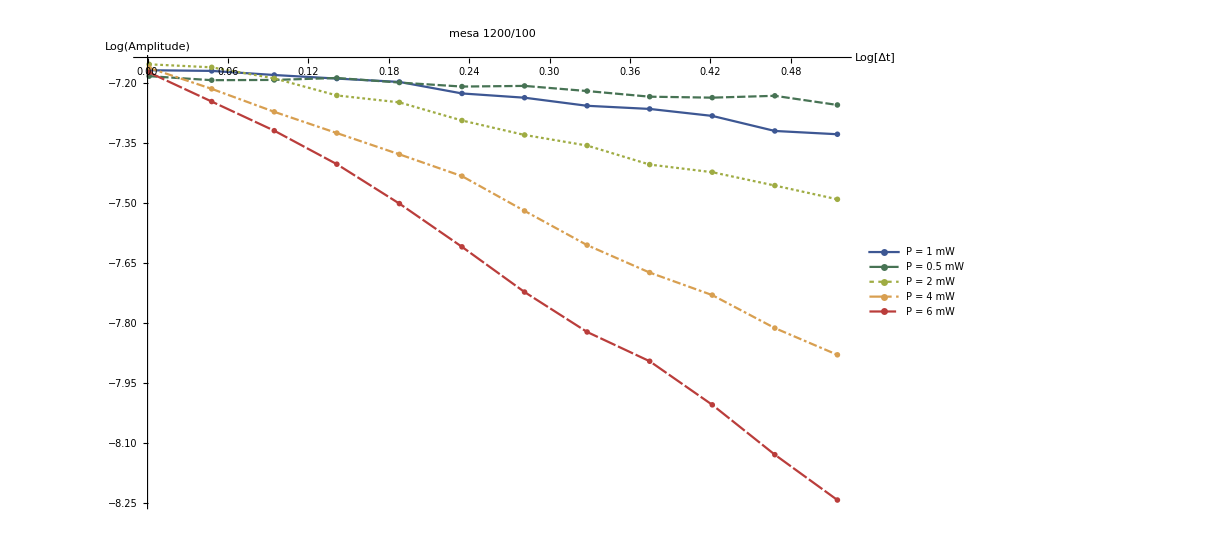

```mathematica
ListLinePlot[Table[perfectPart[[i]],{i,1,5}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Log[Δt]","Log(Amplitude)"},LabelStyle->18,PlotRange->All,PlotStyle->"DarkRainbow"]
```

```mathematica
coeff=Table[FindFit[perfectPart[[i]],a t+b,{a,b},t],{i,1,5}]
```

{{a→-0.329088,b→-7.14932},{a→-0.130989,b→-7.17789},{a→-0.69146,b→-7.13222},{a→-1.4215,b→-7.13303},{a→-2.0987,b→-7.13021}}

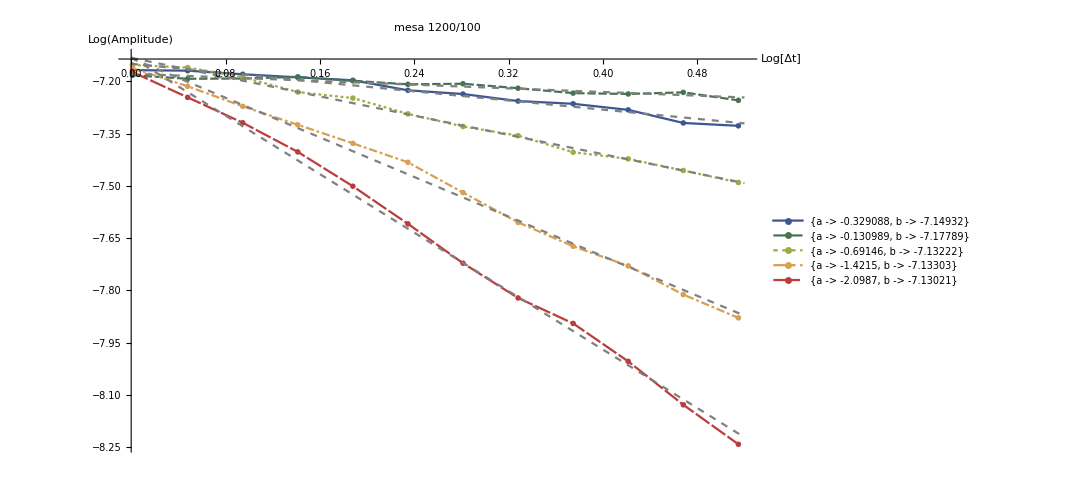

```mathematica
Show[ListLinePlot[Table[perfectPart[[i]],{i,1,5}],PlotLegends->Table[ToString@coeff[[i]],{i,1,5}],ImageSize->800,PlotLabel->"mesa 1200/100",AxesLabel->{"Log[Δt]","Log(Amplitude)"},LabelStyle->18,PlotStyle->"DarkRainbow"],Plot[Table[a x+b/.coeff[[i]],{i,1,5}],{x,0,.52},PlotStyle->{Dashed,Gray}],PlotRange->All]
```

```mathematica
power={1,0.5,2,4,6,0.25}
```

{1,0.5,2,4,6,0.25}

```mathematica
powerNew = Sort[Table[{power[[i]],coeff[[i,1,2]]},{i,1,5}]]
```

{{0.5,-0.130989},{1,-0.329088},{2,-0.69146},{4,-1.4215},{6,-2.0987}}

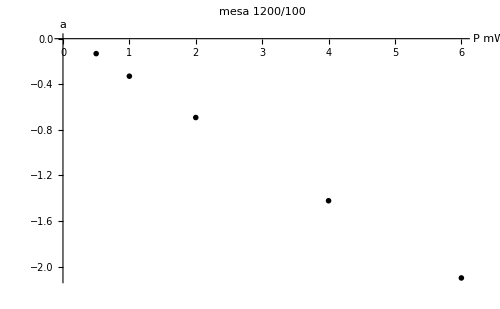

```mathematica
ListPlot[Sort[Table[{power[[i]],coeff[[i,1,2]]},{i,1,5}]],ImageSize->500,PlotLabel->"mesa 1200/100",AxesLabel->{"P mW","a"},LabelStyle->15,AxesStyle->Thick]
```

## Линейная аппроксимация

```mathematica
coefNew = FindFit[powerNew,a t + b,{a,b},t]
```

{a→-0.35779,b→0.0316842}

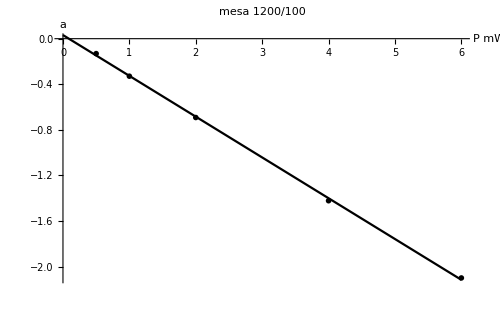

```mathematica
Show[ListPlot[Sort[Table[{power[[i]],coeff[[i,1,2]]},{i,1,5}]],ImageSize->500,PlotLabel->"mesa 1200/100",AxesLabel->{"P mW","a"},LabelStyle->15,AxesStyle->Thick],
Plot[a x + b/.coefNew,{x,0,6}]]
```